```mathematica
ClearAll[Evaluate[Context[]<>"*"]];
(*Clear[];*)
AutoCollapse[]:=(If[$FrontEnd=!=$Failed,SelectionMove[EvaluationNotebook[],All,GeneratedCell];
FrontEndTokenExecute["SelectionCloseUnselectedCells"]]);
HideText[x_]:=(Print[x];AutoCollapse[]);
HideText["Clear Data..."];
```

Clear Data...

```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,nicefrac,esint,siunitx}"},"Magnification"->1.5];

MyTeX[x_]:=HideText[MaTeX[x]];
HideText["Load MaTeX..."]
```

Load MaTeX...

```mathematica
data=ImportString["0.00\t2.25
200.00\t2.35
399.85\t2.47
599.77\t2.58
799.74\t2.70
999.81\t2.81
1199.80\t2.92
1399.95\t3.04
1600.11\t3.15
1800.18\t3.25
","TSV"];
Print["Data Entry Session. Number of Points: ",Length[data]]
AutoCollapse[]
```

Data Entry Session. Number of Points: 10

```mathematica
<<ErrorBarPlots`
```

```mathematica
fit=LinearModelFit[data,x,x]
```

FittedModel[2.24536+0.000562978 x]

```mathematica
yError=√((0.02/(√3))^2+(0.05/(√3))^2)
```

0.0310913

```mathematica
dataWithError=Table[{data[[i]],ErrorBar[.02,.03]},{i,1,Length[data]}];
```

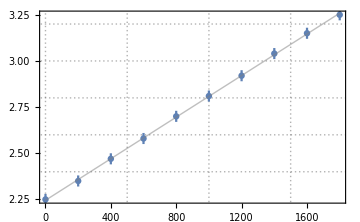

```mathematica
dataplot=Show[ErrorListPlot[dataWithError,
(*PlotMarkers->{"+",16},*)
PlotTheme->"Detailed",
FrameLabel->{
MaTeX["\\nicefrac{m}{\\si{\\g}}"(*,Magnification->1.2*)],
MaTeX["\\nicefrac{\\bar{r}}{\\si{\\mm}}"(*,Magnification->1.5*)]},
ImageSize->Medium,
GridLines->{Range[0,1500,500],Range[2,3.4,.2]},
ImageMargins->{{0,40},{0,0}}],
Plot[Normal[fit],{x,0,Max[dataᵀ[[1]]]},PlotStyle->Directive[Gray,Opacity[.5],Thin]]];
Magnify[%,1.3]
SetDirectory@NotebookDirectory[];
Export["dataplot.pdf",dataplot];
```

```mathematica
SystemOpen["dataplot.pdf"]
```

```mathematica
r=Correlation[dataᵀ[[1]],dataᵀ[[2]]]
```

0.99988

```mathematica
NumberForm[r,8]
```

0.9998796

```mathematica
fit["BestFitParameters"][[2]]//ScientificForm
```

5.62978×10^-4

```mathematica
√((1/r^2-1)/(Length[data]-2))
```

0.00548677

```mathematica
√((1/r^2-1)/(Length[data]-2))*100
```

0.548677

```mathematica
errorByFit=fit["BestFitParameters"][[2]]*√((1/r^2-1)/Length[data])
```

2.76282×10^-6

```mathematica
errorByMeasurement=(.03)/(√Total[(dataᵀ[[1]]-Mean[dataᵀ[[1]]])^2])
```

0.0000165129

```mathematica
√(errorByFit^2+errorByMeasurement^2)//ScientificForm
```

1.67425×10^-5

```mathematica
(4*9.8*79.7/100)/(π*((.336)/1000)^2*fit["BestFitParameters"][[2]]*10^-3/10^-3)
```

1.56468×10^11